```mathematica
Clear["Global`*"]
```

```mathematica
(*Built-in functions. *)
(*RowDelete takes a matrix and deletes the specified rows*)
RowDelete[x_,entries_]:=Module[{list,i},
list=Table[{entries[[i]]},{i,1,Length[entries]}];
Delete[x,list]
]
(*ColumnDelete takes a matrix and delete the specified columns*)
ColumnDelete[x_,entries_]:=Module[{},
Transpose[RowDelete[Transpose[x],entries]]
]
(*AddZeroToRow adds a zero to a row vector*)
AddZeroToRow[x_,j_]:=Module[{l},
l=Length[x];
Join[Take[x,j-1],{0},Take[x,-(l-j+1)]]
]
(*AddZerosToRow will add any number of zeros to a row vector*)
AddZerosToRow[x_,entries_]:=Module[{y,list,i},
y=x;
list=Sort[entries];
For[i=1,i≤Length[list],i++,
y=AddZeroToRow[y,list[[i]]]
];
y
]
(*Composite constrained and unconstrained estimates with covatiares. I.e., the most general case.*)
MAR[datasets_, cov_, constraints_]:=Module[{X,U,Y,Z,D,d0,p,x0,u0,y0,one,popdata,covdata,tanks,tankrow,index,tempdata,c,j,k},
p=Length[datasets[[1,1]]]-cov;

If[cov==0,
X={};Y={};
For[j=1,j≤Length[datasets],j++,
x0=Delete[datasets[[j]],Length[datasets[[j]]]];
y0=Delete[datasets[[j]],1];
X=Join[X,x0];
Y=Join[Y,y0]
];
one={Table[1,{i,1,Length[X]}]};
Z=Transpose[Join[one,Transpose[X]]];
D={};
For[k=1,k≤p,k++,
c={};
For[j=1,j≤p,j++,
c=Join[c,If[MemberQ[constraints,{k,j}],{j},{}]]
];
d0={AddZerosToRow[Flatten[{Y[[All,k]]}.ColumnDelete[Z,c+1].Inverse[Transpose[ColumnDelete[Z,c+1]].ColumnDelete[Z,c+1]]],c+1]};
D=Join[D,d0]
];
D,

X={};Y={};U={};
For[j=1,j≤Length[datasets],j++,
tempdata=datasets[[j]];
x0=tempdata[[All,cov+1;;cov+p]];
x0=Delete[x0,Length[x0]];
u0=tempdata[[All,1;;cov]];
u0=Delete[u0,Length[u0]];
y0=tempdata[[All,cov+1;;cov+p]];
y0=Delete[y0,1];

X=Join[X,x0];
U=Join[U,u0];
Y=Join[Y,y0];
];
one={Table[1,{i,1,Length[X]}]};
Z=Transpose[Join[one,Transpose[U],Transpose[X]]];
D={};
For[k=1,k≤p,k++,
c={};
For[j=1,j≤p,j++,
c=Join[c,If[MemberQ[constraints,{k,j}],{j},{}]]
];
d0={AddZerosToRow[Flatten[{Y[[All,k]]}.ColumnDelete[Z,c+1+cov].Inverse[Transpose[ColumnDelete[Z,c+1+cov]].ColumnDelete[Z,c+1+cov]]],c+1+cov]};
D=Join[D,d0]
];
D
]
]
(*Code to process raw data after it has been imported.*)
ProcessData[raw_,cov_]:=Module[{rawdata,p,tankrow,tanks,purepopdata,logpopdata,covdata,processeddata,index,compdataset,i,i0,j,data},
rawdata=Delete[raw,1];
p=Length[rawdata[[1]]]-cov-1;

tankrow=Delete[raw[[All,1]],1];(*extracts the column of tank labels as a row vector.*)
tanks=DeleteDuplicates[tankrow];(*Just getting a list of tank labels*)

purepopdata=ColumnDelete[rawdata,{1}];
For[i=1,i≤cov,i++,
purepopdata=ColumnDelete[purepopdata,{1}]
];
logpopdata=Log[purepopdata];

If[cov==0,covdata={},
covdata=ColumnDelete[rawdata,{1}];
For[i=1,i≤p,i++,
covdata=ColumnDelete[covdata,{Length[covdata[[1]]]}]
]
];

processeddata=If[cov==0,Transpose[Join[{tankrow},Transpose[logpopdata]]],Transpose[Join[{tankrow},Transpose[covdata],Transpose[logpopdata]]]];(*Join log transformed values back up with tank labels*)

(*Below we extract tank specific processed data and label it by the tank label.*)
For[j=1,j≤Length[tanks],j++,
index=tanks[[j]];
data[index]={};
For[i=1,i≤Length[processeddata],i++,
i0=If[processeddata[[i,1]]==index,{processeddata[[i]]},{}];
data[index]=Join[data[index],i0]
];
data[index]=ColumnDelete[data[index],{1}]
];

compdataset={};
For[j=1,j≤Length[tanks],j++,
index=tanks[[j]];
compdataset=Join[compdataset,{data[index]}]
];
compdataset
]
(*Script to get sensitivity measures from the matrix output of MAR
and relative interaction strengths*)
B[D_]:=Module[{p,cov,B},(*extract B matrix*)
p=Length[D];
cov=Length[D[[1]]]-p-1;
B=D[[All,2+cov;;1+cov+p]]
]

Sens[D_]:=Module[{p,cov,B,det,eig},
p=Length[D];
cov=Length[D[[1]]]-p-1;
B=D[[All,2+cov;;1+cov+p]];
det=Det[B];
eig=Abs[Eigenvalues[B]][[1]];
{(det^2)^(1/p),eig,1/(1-eig^2)}
]

RIS[D_]:=Module[{p,cov,B,erow,e1,e2,e3,e4,rel}, (*row: top down control*)
p=Length[D];
cov=Length[D[[1]]]-p-1;
B=D[[All,2+cov;;1+cov+p]];
erow=B[[-2]];(*Extract second to last row in B matrix*)
e1=Abs[Delete[erow,-2]];(*Delete second to last entry in erow (diagonal)*)
e2=Sort[e1];(*sorts small to large*)
e3=Delete[e2,-1];(*delete largest value*)
e4=Mean[e3];(*average of smaller values*)
rel=e4/Max[e1](*average/largest*)
]

RISd[D_]:=Module[{p,cov,B,erow,e2,e3,e4,rel}, (*row: top down control with diagonal entry*)
p=Length[D];
cov=Length[D[[1]]]-p-1;
B=D[[All,2+cov;;1+cov+p]];
erow=B[[-2]];(*Extract second to last row in B matrix*)
e2=Abs[Sort[erow]];(*sorts small to large absolute value*)
e3=Delete[e2,-1];(*delete largest value*)
e4=Mean[e3];(*average of smaller values*)
rel=e4/Max[e2](*average/largest*)
]

bRIS[D_]:=Module[{p,cov,B,ecol,e1,e2,e3,e4,rel}, (*column: bottom up control*)
p=Length[D];
cov=Length[D[[1]]]-p-1;
B=D[[All,2+cov;;1+cov+p]];
ecol=B[[All,-2]];(*Extract second to last column in B matrix*)
e1=Abs[Delete[ecol,-2]];(*Delete second to last entry in erow (diagonal)*)
e2=Sort[e1];(*sorts small to large*)
e3=Delete[e2,-1];(*delete largest value*)
e4=Mean[e3];(*average of smaller values*)
rel=e4/Max[e1](*average/largest*)
]

bRISd[D_]:=Module[{p,cov,B,ecol,e2,e3,e4,rel}, (*column: bottom up control with diagonal entry*)
p=Length[D];
cov=Length[D[[1]]]-p-1;
B=D[[All,2+cov;;1+cov+p]];
ecol=B[[All,-2]];(*Extract second to last column in B matrix*)
e2=Abs[Sort[ecol]];(*sorts small to large*)
e3=Delete[e2,-1];(*delete largest value*)
e4=Mean[e3];(*average of smaller values*)
rel=e4/Max[e2](*average/largest*)
]

CV[Q_]:=Module[{c1,Hs,meanHs,totalHs,wHs,popCV,wCVpop,wAvg,comm,commCV},
c1=Delete[rawdata[Q],1];
Hs=c1[[All,2;;-3]];(*This will only work for 0 cov treatments, it extracts the herbivore columns*)
meanHs=Total[Hs]/Length[Hs];(*total of each herbivore species down column / # of rows*)
totalHs=Total[meanHs];
(*Adds the mean of each herbivore species together*)
wHs=meanHs/totalHs;
(*This gives the weight of each species*)
popCV=StandardDeviation[Hs]/Mean[Hs];
wCVpop=popCV*wHs;(*weighted population CV*)
wAvg=Total[wCVpop];(*weighted average*)

comm=Total[Hs,{2}];(*totals hs by row = total herbivore*)
commCV=StandardDeviation[comm]/Mean[comm];
{wAvg,commCV}
]
```

```mathematica
SetDirectory["/Users/JayneEllen/Dropbox/Weak interactions/tank data"];

(*Import various multi-tank data sets some with covariates, some without.*)
(*0 covariates*)
rawdata[1]=Import["CER0.csv"];
rawdata[2]=Import["CER_DAP0.csv"];
rawdata[3]=Import["CER_SCA0.csv"];
rawdata[4]=Import["DAP0.csv"];
rawdata[5]=Import["DAPSCA0.csv"];
rawdata[6]=Import["SCA0.csv"];
rawdata[7]=Import["N0.csv"];
rawdata[8]=Import["N_CER0.csv"];
rawdata[9]=Import["N_CER_DAP0.csv"];
rawdata[10]=Import["N_CER_SCA0.csv"];
rawdata[11]=Import["N_DAP0.csv"];
rawdata[12]=Import["N_SCA0.csv"];
rawdata[13]=Import["N_SCA_DAP0.csv"];
rawdata[14]=Import["N_I_DAP0.csv"];
rawdata[15]=Import["N_I0.csv"];
rawdata[16]=Import["N_I_COP0.csv"];
rawdata[17]=Import["CER_SCA_DAP0.csv"];

(*1 covariate*)
rawdata[18]=Import["CER.csv"];
rawdata[19]=Import["CER_DAP.csv"];
rawdata[20]=Import["CER_SCA.csv"];
rawdata[21]=Import["DAP.csv"];
rawdata[22]=Import["DAPSCA.csv"];
rawdata[23]=Import["SCA.csv"];
rawdata[24]=Import["N.csv"];
rawdata[25]=Import["N_CER.csv"];
rawdata[26]=Import["N_CER_DAP.csv"];
rawdata[27]=Import["N_CER_SCA.csv"];
rawdata[28]=Import["N_Dap.csv"];
rawdata[29]=Import["N_Sca.csv"];
rawdata[30]=Import["N_SCA_DAP.csv"];
rawdata[31]=Import["N_I_DAP.csv"];

(*2 covariates*)
rawdata[32]=Import["N_I.csv"];
rawdata[33]=Import["N_I_cop.csv"];

comm={"c","cd","cs","d","ds","s","N","N-c","N-cd","N-cs","N-d","N-s","N-ds","NI-d","NI","NIcop","csd"};
```

```mathematica
For[i=1,i≤17,i++,
prodata[i]=ProcessData[rawdata[i],0];
m[i]=MAR[prodata[i],0,{}]
]
```

```mathematica
MM={};
For[i=1,i≤17,i++,
tanks=Length[prodata[i]];
MM=Join[MM,{Table[MAR[{prodata[i][[j]]},0,{}],{j,1,tanks}]}]
]
```

### Species count and stability, RIS, measures

```mathematica
(*composite measurements*)
cpdet={};
cpeig={};
cpRIS={};
cpRISd={};
cpbRIS={};
cpbRISd={};
cRISdet={};
cRISeig={};
cRISddet={};
cRISdeig={};
cbRISdet={};
cbRISeig={};
cbRISddet={};
cbRISdeig={};

For[i=1,i≤17,i++,
p=Length[m[i]];
det=Sens[m[i]][[1]];
eig=Sens[m[i]][[2]];
rel=RIS[m[i]];
reld=RISd[m[i]];
brel=bRIS[m[i]];
breld=bRISd[m[i]];
cpdet=Join[cpdet,{Style[{p,det},Hue[(i +1)/17]]}];
cpeig=Join[cpeig,{Style[{p,eig},Hue[(i +1)/17]]}];
cpRIS=Join[cpRIS,{Style[{p,rel},Hue[(i +1)/17]]}];
cpRISd=Join[cpRISd,{Style[{p,reld},Hue[(i +1)/17]]}];
cpbRIS=Join[cpbRIS,{Style[{p,brel},Hue[(i +1)/17]]}];
cpbRISd=Join[cpbRISd,{Style[{p,breld},Hue[(i +1)/17]]}];
cRISdet=Join[cRISdet,{Style[{rel,det},Hue[(i +1)/17]]}];
cRISeig=Join[cRISeig,{Style[{rel,eig},Hue[(i +1)/17]]}];
cRISddet=Join[cRISddet,{Style[{reld,det},Hue[(i +1)/17]]}];
cRISdeig=Join[cRISdeig,{Style[{reld,eig},Hue[(i +1)/17]]}];
cbRISdet=Join[cbRISdet,{Style[{brel,det},Hue[(i +1)/17]]}];
cbRISeig=Join[cbRISeig,{Style[{brel,eig},Hue[(i +1)/17]]}];
cbRISddet=Join[cbRISddet,{Style[{breld,det},Hue[(i +1)/17]]}];
cbRISdeig=Join[cbRISdeig,{Style[{breld,eig},Hue[(i +1)/17]]}];
]

(*tank measurements*)
tpdet={};
tpeig={};
tpRIS={};
tpRISd={};
tpbRIS={};
tpbRISd={};
tRISdet={};
tRISeig={};
tRISddet={};
tRISdeig={};
tbRISdet={};
tbRISeig={};
tbRISddet={};
tbRISdeig={};

For[i=1,i≤17,i++,
tanks=Length[prodata[i]];
For[j=1,j≤tanks,j++,
p=Length[MM[[i,j]]];(*i=treatment [rawdata i], j=tank from rawdata i*)
det=Sens[MM[[i,j]]][[1]];
eig=Sens[MM[[i,j]]][[2]];
rel=RIS[MM[[i,j]]];
reld=RISd[MM[[i,j]]];
brel=bRIS[MM[[i,j]]];
breld=bRISd[MM[[i,j]]];
tpdet=Join[tpdet,{Style[{p,det},Hue[(i+1)/17]]}];
tpeig=Join[tpeig,{Style[{p,eig},Hue[(i +1)/17]]}];
tpRIS=Join[tpRIS,{Style[{p,rel},Hue[(i+1)/17]]}];
tpRISd=Join[tpRISd,{Style[{p,reld},Hue[(i+1)/17]]}];
tpbRIS=Join[tpbRIS,{Style[{p,brel},Hue[(i+1)/17]]}];
tpbRISd=Join[tpbRISd,{Style[{p,breld},Hue[(i+1)/17]]}];
tRISdet=Join[tRISdet,{Style[{rel,det},Hue[(i +1)/17]]}];
tRISeig=Join[tRISeig,{Style[{rel,eig},Hue[(i +1)/17]]}];
tRISddet=Join[tRISddet,{Style[{reld,det},Hue[(i +1)/17]]}];
tRISdeig=Join[tRISdeig,{Style[{reld,eig},Hue[(i +1)/17]]}];
tbRISdet=Join[tbRISdet,{Style[{brel,det},Hue[(i +1)/17]]}];
tbRISeig=Join[tbRISeig,{Style[{brel,eig},Hue[(i +1)/17]]}];
tbRISddet=Join[tbRISddet,{Style[{breld,det},Hue[(i +1)/17]]}];
tbRISdeig=Join[tbRISdeig,{Style[{breld,eig},Hue[(i +1)/17]]}];
]
]
```

Species count, λ

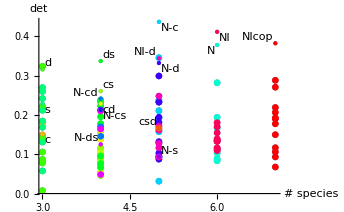

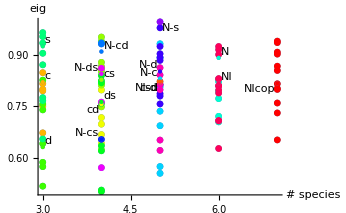

Species count, top↓ relative interaction strength

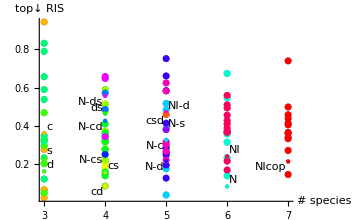

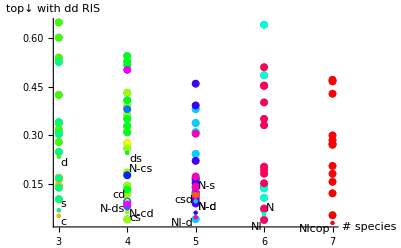

Species count, bottom↑ relative interaction strength

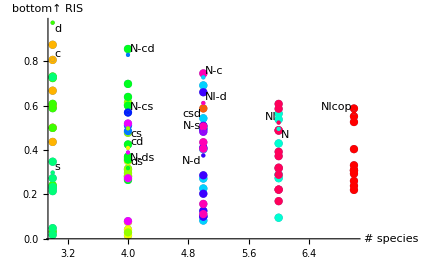

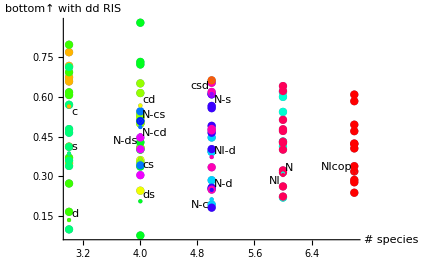

top↓ relative interaction strength, λ

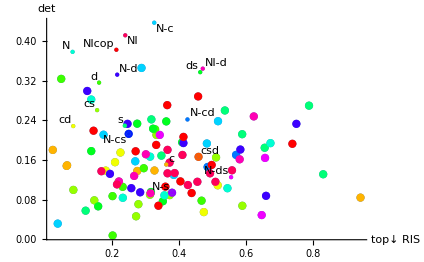

```mathematica
Style["
Species count, λ",FontSize->20]
Show[ListPlot[tpdet],ListPlot[MapThread[Labeled,{cpdet,comm}],PlotStyle->PointSize[Large]],AxesLabel->{"# species","det"},PlotRange->All]
Show[ListPlot[tpeig],ListPlot[MapThread[Labeled,{cpeig,comm}],PlotStyle->PointSize[Large]],AxesLabel->{"# species","eig"},PlotRange->All]

Style["
Species count, top↓ relative interaction strength",FontSize->20]
Show[ListPlot[tpRIS],ListPlot[MapThread[Labeled,{cpRIS,comm}],PlotStyle->PointSize[Large]],AxesLabel->{"# species","top↓ RIS"},PlotRange->All]
Show[ListPlot[tpRISd],ListPlot[MapThread[Labeled,{cpRISd,comm}],PlotStyle->PointSize[Large]],AxesLabel->{"# species","top↓ with dd RIS"},PlotRange->All]

Style["
Species count, bottom↑ relative interaction strength",FontSize->20]
Show[ListPlot[tpbRIS],ListPlot[MapThread[Labeled,{cpbRIS,comm}],PlotStyle->PointSize[Large]],AxesLabel->{"# species","bottom↑ RIS"},PlotRange->All]
Show[ListPlot[tpbRISd],ListPlot[MapThread[Labeled,{cpbRISd,comm}],PlotStyle->PointSize[Large]],AxesLabel->{"# species","bottom↑ with dd RIS"},PlotRange->All]


Style["
top↓ relative interaction strength, λ",FontSize->20]
Show[ListPlot[tRISdet],ListPlot[MapThread[Labeled,{cRISdet,comm}],PlotStyle->PointSize[Large]],AxesLabel->{"top↓ RIS","det"},PlotRange->All]
```